## Noisy Symbolic Arnoldi

### Iteration 1

```mathematica
A = ({{α, 0}, {0, β}});
H = ({{0, 0}, {0, 0}, {0, 0}});
Subscript[q, 1] = {1,0};
Subscript[q, 2] = A.Subscript[q, 1]+{Subscript[ξ, 1,1],Subscript[ξ, 1,2]}
H[[1,1]] = Subscript[q, 1].Subscript[q, 2];
Subscript[q, 2] = Subscript[q, 2] - H[[1,1]]*Subscript[q, 1];
H[[2,1]] = √(Subscript[q, 2].Subscript[q, 2]);
H[[2,1]] = Subscript[ξ, 1,2];
Subscript[q, 2] = Subscript[q, 2]/H[[2,1]];
(*Subscript[σ, 1] = Eigenvalues[H[[1,1]]]*)
Subscript[σ, 1] = H[[1,1]];

Subscript[q, 3] = A.Subscript[q, 2] + {Subscript[ξ, 2,1],Subscript[ξ, 2,2]}
H[[1,2]] =Subscript[q, 1].Subscript[q, 3];
H[[2,2]] = Subscript[q, 2].Subscript[q, 3];
Subscript[q, 3] = Subscript[q, 3] - H[[1,2]] Subscript[q, 1];
Subscript[q, 3] = Subscript[q, 3] - H[[2,2]] Subscript[q, 2];
H[[3,2]] = √(Subscript[q, 3].Subscript[q, 3]);
Subscript[σ, 2] = Eigenvalues[H[[1;;2]]];
H //MatrixForm
```

{α+ξ_(1,1),ξ_(1,2)}

{ξ_(2,1),β+ξ_(2,2)}

(α+ξ_(1,1) | ξ_(2,1)
ξ_(1,2) | β+ξ_(2,2)
0 | 0)

```mathematica
Subscript[q, 2]
```

{0,1}

(α+ξ_(1,1) | ξ_(2,1)
ξ_(1,2) | β+ξ_(2,2)
0 | 0)

### Taylor Series Expansion

```mathematica
a=Series[Subscript[σ, 2][[1]],{Subscript[ξ, 1,1],0,3},{Subscript[ξ, 1,2],0,3},{Subscript[ξ, 2,1],0,3},{Subscript[ξ, 2,2],0,3}];
```

```mathematica
a = Normal[Simplify[a]];
```

```mathematica
b=Series[Subscript[σ, 2][[2]],{Subscript[ξ, 1,1],0,3},{Subscript[ξ, 1,2],0,3},{Subscript[ξ, 2,1],0,3},{Subscript[ξ, 2,2],0,3}];
```

```mathematica
b=Normal[Simplify[b]];
```

Now we take the expected value of the above value.  Remember E[ξ] = E [ξ^2] = 0, and E[ξ^2] = Var[ξ].  This first formula greatly simplifies the expression.

```mathematica
expectedValue = {0,0};
```

```mathematica
f[α_,β_]=1/2 (α-√((α-β)^2)+β)+(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) Subscript[ξ, 1,1]^2)/(α-β)^6) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2+((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) Subscript[ξ, 1,1]^2)/(α-β)^8) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2 Subscript[ξ, 2,2]^2
```

1/2 (α-√((α-β)^2)+β)+(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ_(1,1)^2)/(α-β)^6) ξ_(1,2)^2 ξ_(2,1)^2+((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ_(1,1)^2)/(α-β)^8) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2

```mathematica
expectedValue[[1]]=f[α,β]
```

1/2 (α-√((α-β)^2)+β)+(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ_(1,1)^2)/(α-β)^6) ξ_(1,2)^2 ξ_(2,1)^2+((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ_(1,1)^2)/(α-β)^8) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2

```mathematica
g[α_,β_]=1/2 (α+√((α-β)^2)+β)-(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) Subscript[ξ, 1,1]^2)/(α-β)^6) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2-((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) Subscript[ξ, 1,1]^2)/(α-β)^8) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2 Subscript[ξ, 2,2]^2
```

1/2 (α+√((α-β)^2)+β)-(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ_(1,1)^2)/(α-β)^6) ξ_(1,2)^2 ξ_(2,1)^2-((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ_(1,1)^2)/(α-β)^8) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2

```mathematica
expectedValue[[2]] =g[α,β]
```

1/2 (α+√((α-β)^2)+β)-(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ_(1,1)^2)/(α-β)^6) ξ_(1,2)^2 ξ_(2,1)^2-((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ_(1,1)^2)/(α-β)^8) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2

```mathematica
expectedValue//MatrixForm
```

(1/2 (α-√((α-β)^2)+β)+(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ_(1,1)^2)/(α-β)^6) ξ_(1,2)^2 ξ_(2,1)^2+((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ_(1,1)^2)/(α-β)^8) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2
1/2 (α+√((α-β)^2)+β)-(1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ_(1,1)^2)/(α-β)^6) ξ_(1,2)^2 ξ_(2,1)^2-((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ_(1,1)^2)/(α-β)^8) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2)

```mathematica
Subscript[ξ, 1,1]:=√ξ
Subscript[ξ, 1,2]:=√ξ
Subscript[ξ, 2,1]:=√ξ
Subscript[ξ, 2,2]:=√ξ
```

```mathematica
F[α_,β_,ξ_]=f[α,β]
```

1/2 (α-√((α-β)^2)+β)+ξ^3 ((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ)/(α-β)^8)+ξ^2 (1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ)/(α-β)^6)

```mathematica
G[α_,β_,ξ_]=g[α,β]
```

1/2 (α+√((α-β)^2)+β)-ξ^3 ((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ)/(α-β)^8)-ξ^2 (1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ)/(α-β)^6)

```mathematica
expectedValue//MatrixForm
```

(1/2 (α-√((α-β)^2)+β)+ξ^3 ((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ)/(α-β)^8)+ξ^2 (1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ)/(α-β)^6)
1/2 (α+√((α-β)^2)+β)-ξ^3 ((6 √((α-β)^2))/(α-β)^6+(90 √((α-β)^2) ξ)/(α-β)^8)-ξ^2 (1/(((α-β)^2)^(3/2))+(6 √((α-β)^2) ξ)/(α-β)^6))

```mathematica
Manipulate[Plot[{F[α,β,ξ],β, G[α,β,ξ],α},{ξ,0,50},PlotRange->{-20,20},PlotStyle->{{Red, Thick},{Red},{Blue, Thick},{Blue}},AxesLabel->{"ξ","Eigenvalue"}],{{α,10},-10,10},{{β,1},-10,10}]
```

```mathematica
Manipulate[Plot[{F[α,β,ξ],β, G[α,β,ξ],α},{α,0,10},PlotRange->{-15,15}
,PlotStyle->{{Red, Thick},{Red},{Blue, Thick},{Blue}},AxesLabel->{"α","Eigenvalue"}],{{β,5},0,10},{ξ,0,1}]
```

## Correlated Noise

```mathematica
Subscript[ξ, 1,1]:=ξ
Subscript[ξ, 1,2]:=ξ
Subscript[ξ, 2,1]:=ξ
Subscript[ξ, 2,2]:=ξ
```

```mathematica
Subscript[σ, 2]//MatrixForm
```

(1/2 (α+β+2 ξ-√((-α-β-2 ξ)^2-4 (α β+α ξ+β ξ)))
1/2 (α+β+2 ξ+√((-α-β-2 ξ)^2-4 (α β+α ξ+β ξ))))

```mathematica
Limit[Subscript[σ, 2], ξ->-0.1]//MatrixForm
```

(-0.1+0.5 α+0.5 β-0.5 √(0.04+1. α^2-2. α β+1. β^2)
-0.1+0.5 α+0.5 β+0.5 √(0.04+1. α^2-2. α β+1. β^2))

```mathematica
σ[α_,β_,ξ_] = Eigenvalues[H[[1;;2]]]
```

{1/2 (α+β+2 ξ-√(α^2-2 α β+β^2+4 ξ^2)),1/2 (α+β+2 ξ+√(α^2-2 α β+β^2+4 ξ^2))}

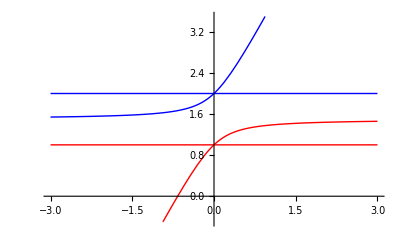

```mathematica
Plot[{σ[1,2,ξ][[1]],σ[1,2,ξ][[2]], 1, 2},{ξ,-3,3}, PlotStyle->{{Red, Thick}, {Blue, Thick},{Red},{Blue}}]
```

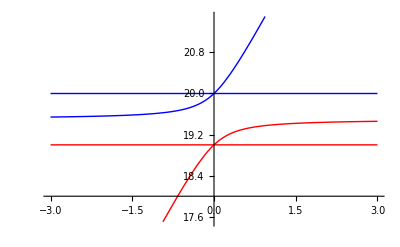

```mathematica
Plot[{σ[19,20,ξ][[1]],19,σ[20,19,ξ][[2]], 20},{ξ,-3,3}, PlotStyle->{{Red, Thick},{Red}, {Blue, Thick},{Blue}}]
```